## Term Project - Fourier

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mark\Documents\School\PHSCS230\TermProject

```mathematica
birdsound1 = Import["eagle.mp3"];
birdsound2 = Import["babybird.mp3"];
birdsound3 = Import["birdcall.mp3"];
bigcat1=Import["bigcat1.mp3"];
bigcat2=Import["bigcat2.mp3"];
bigcat3=Import["bigcat3.mp3"];
g =ExampleData[{"Sound", "B"}];
soundlist={birdsound1,birdsound2,birdsound3,bigcat1,bigcat2,bigcat3};
```

```mathematica
frenchHorn=ExampleData[{"Sound", "FrenchHornScale"}];
tuba =ExampleData[{"Sound", "TubaScale"}];
trumpet=ExampleData[{"Sound", "TrumpetScale"}];
piano=ExampleData[{"Sound", "PianoScale"}];
viola=ExampleData[{"Sound", "ViolaScale"}];
violin =ExampleData[{"Sound", "ViolinScale"}];
```

```mathematica
truncate[data_,f_]:=Module[{i,j},{i,j}=Floor[Dimensions[data]/Sqrt[f]];
PadRight[Take[data,i,j],Dimensions[data],0.]];
```

```mathematica
myaudio=frenchHorn

rate= myaudio//AudioSampleRate//QuantityMagnitude; (* samplerate in Hz *)
duration = myaudio//Duration//QuantityMagnitude ;(* duration in seconds *)
ampdata = myaudio//AudioData;
ampdata =  If[Length[Dimensions[ampdata]]>1,ampdata[[1]],ampdata];
samplenum =ampdata//Length; (* number of samples *)

timerange = duration; (* maximum time in seconds *)
timestep = duration/samplenum//N; (* time step in seconds *)
freqrange = rate/2//N; (* maximum frequency in Hz *)
freqstep=freqrange/samplenum//N; (* frequency step in Hz *)

Print["rate = ", rate, ", samplenum = ", samplenum, ", timestep = ", timestep, ", timerange = ", timerange, ", freqstep = ", freqstep, ", freqrange = ", freqrange]

chunksize =Min[1000,samplenum/50];
chunkcount = Min[Floor[samplenum/chunksize],50];
Print["chunksize = ",chunksize,", chunkcount = ",chunkcount];
ListAnimate[Table[ListPlot[ampdata[[(n-1)*chunksize+1;;n*chunksize]],Joined->True,Frame->True,PlotRange->All],{n,1,chunkcount}]]


rawspectrum = FourierDCT[ampdata]; (* raw discrete Fourier transform *)
ListPlot[rawspectrum,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->All,AspectRatio->1/6]

goodrange[rawspectraldata_,threshold_] := Module[{len,absdata,maxabs,blocksize,blockmaxvals,maxresiduals,threshhold,maxlargenough,falsepositions,cutoff},
len = rawspectraldata//Length;
absdata = rawspectraldata//Abs;
maxabs=absdata//Abs//Max;
blocksize =Min[Ceiling[len/10000],100];
blockmaxvals =Max/@Partition[absdata,blocksize];
maxresiduals = Table[blockmaxvals[[i;;]]//Max,{i,Length[blockmaxvals]}];
maxlargenough=(#>maxabs*threshold)&/@maxresiduals;
falsepositions = Position[maxlargenough,False];
cutoff = If[Length[falsepositions]>0,Min[1.1*falsepositions[[1,1]]*blocksize//Ceiling,samplenum],samplenum];
cutoff*freqstep
]
freqmax = goodrange[rawspectrum,0.05]

(* Plot the abs value of the spectrum. If you don't like the freqmax value obtained above, set it to whatever you prefer. *)
ListPlot[rawspectrum//Abs,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->{{1,freqmax},All}]
Position[rawspectrum//Abs,Max[rawspectrum //Abs]]*.0477
```

-Graphics-

rate = 22050, samplenum = 277472, timestep = 0.0000453515, timerange = 12.5838, freqstep = 0.0397337, freqrange = 11025.

chunksize = 1000, chunkcount = 50

-Graphics-

1452.67

-Graphics-

{{627.78}}

```mathematica
k = TakeLargest[rawspectrum //Abs, 10]
Position[rawspectrum//Abs,#][[1]][[1]]&/@k*freqstep
```

{15.8018,15.3874,15.2115,14.9637,14.7104,14.2769,14.0276,13.408,13.1525,13.049}

{522.936,522.896,579.676,579.755,547.889,522.975,548.047,579.596,522.856,580.113}

bigcat1, bigcat2, bigcat3

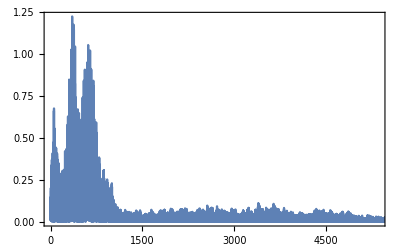
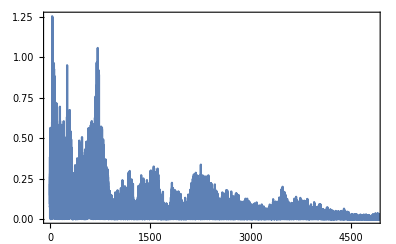
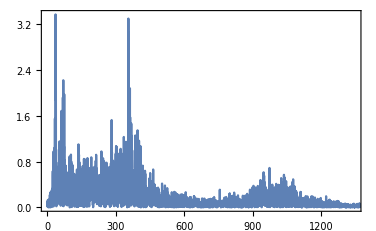

birdsound1 (eagle), birdsound3

```mathematica
-Graphics--Graphics-
```

French Horn, trumpet, tuba

```mathematica
-Graphics--Graphics--Graphics-
```

piano, viola, violin

```mathematica
-Graphics--Graphics--Graphics-
```